# ListDensityPlot del indicador de caos 𝒫̄ [Mirkin y Wisniacki 2021]

## L=7

```mathematica
L=7; 
(* Datos del promedio temporal del valor esperado de Haar de la pureza de Choi *)
{#[[1]],chaometerPurity=#[[2;;]];}&[Import["data/chaometer_purity/wisniacki_open_L_"<>ToString[L]<>"_hx_1.csv"]]
```

{{hz,J,pureza del caometro (indicador de Wisniacki)},Null}

```mathematica
Select[chaometerPurity,#[[3]]>=0.85&]
```

{{0.,0.,1.},{0.1,0.,1.},{0.2,0.,1.},{0.3,0.,1.},{0.4,0.,1.},{0.5,0.,1.},{0.6,0.,1.},{0.7,0.,1.},{0.8,0.,1.},{0.9,0.,1.},{1.,0.,1.},{1.1,0.,1.},{1.2,0.,1.},{1.3,0.,1.},{1.4,0.,1.},{1.5,0.,1.},{1.6,0.,1.},{1.7,0.,1.},{1.8,0.,1.},{1.9,0.,1.},{2.,0.,1.},{2.1,0.,1.},{2.2,0.,1.},{2.3,0.,1.},{2.4,0.,1.},{2.5,0.,1.},{2.6,0.,1.},{2.7,0.,1.},{2.7,0.1,0.850887},{2.8,0.,1.},{2.9,0.,1.},{3.,0.,1.},{3.,0.1,0.859539}}

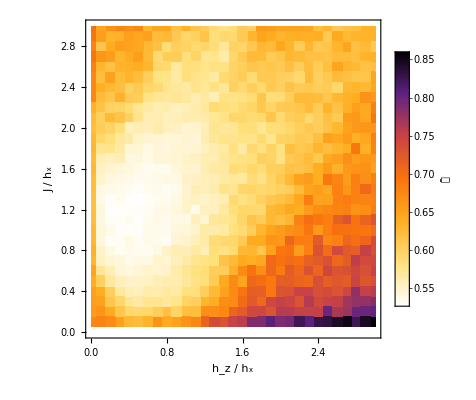

```mathematica
fontSize=18;

fig=ListDensityPlot[chaometerPurity,
ColorFunction->(ColorData["SunsetColors"][1-#]&),ColorFunctionScaling->True,
PlotRange->{Min[chaometerPurity[[;;961,3]]],0.86},
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"𝒫̄",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"},
AspectRatio->1
]
```

```mathematica
filename="figs_ja/chaometer_purity_wisniacki_open_L_"<>ToString[L]<>"_hx_1.pdf";
Export[filename,fig,"PDF",ImageResolution->300]
```

figs_ja/chaometer_purity_wisniacki_open_L_7_hx_1.pdf

```mathematica
RunProcess[{"pdfcrop",filename,filename}]
```

<|ExitCode→0,StandardOutput→PDFCROP 1.42, 2023/04/15 - Copyright (c) 2002-2023 by Heiko Oberdiek, Oberdiek Package Support Group.
==> 1 page written on `figs_ja/chaometer_purity_wisniacki_open_L_7_hx_1.pdf'.
,StandardError→|>

## L=6

```mathematica
L=6; 
(* Datos del promedio temporal del valor esperado de Haar de la pureza de Choi *)
{#[[1]],chaometerPurity=#[[2;;]];}&[Import["data/chaometer_purity/wisniacki_open_L_"<>ToString[L]<>"_hx_1.csv"]]
```

{{hz,J,pureza del caometro (indicador de Wisniacki)},Null}

```mathematica
Select[chaometerPurity,#[[3]]>=0.85&]
```

{{0.,0.,1.},{0.1,0.,1.},{0.2,0.,1.},{0.3,0.,1.},{0.4,0.,1.},{0.5,0.,1.},{0.6,0.,1.},{0.7,0.,1.},{0.8,0.,1.},{0.9,0.,1.},{1.,0.,1.},{1.1,0.,1.},{1.2,0.,1.},{1.3,0.,1.},{1.4,0.,1.},{1.5,0.,1.},{1.6,0.,1.},{1.7,0.,1.},{1.8,0.,1.},{1.9,0.,1.},{2.,0.,1.},{2.1,0.,1.},{2.2,0.,1.},{2.3,0.,1.},{2.4,0.,1.},{2.5,0.,1.},{2.5,0.1,0.857987},{2.6,0.,1.},{2.7,0.,1.},{2.8,0.,1.},{2.9,0.,1.},{3.,0.,1.},{3.,0.1,0.864223}}

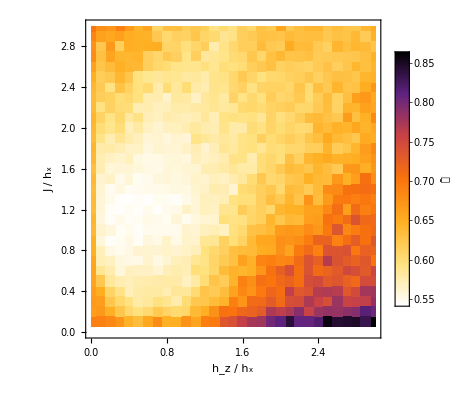

```mathematica
fontSize=18;

fig=ListDensityPlot[chaometerPurity,
ColorFunction->(ColorData["SunsetColors"][1-#]&),ColorFunctionScaling->True,
PlotRange->{Min[chaometerPurity[[;;961,3]]],0.865},
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"𝒫̄",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"},
AspectRatio->1
]
```

```mathematica
filename="figs_ja/chaometer_purity_wisniacki_open_L_"<>ToString[L]<>"_hx_1.pdf";
Export[filename,fig,"PDF",ImageResolution->300]
```

figs_ja/chaometer_purity_wisniacki_open_L_6_hx_1.pdf

```mathematica
RunProcess[{"pdfcrop",filename,filename}]
```

<|ExitCode→0,StandardOutput→PDFCROP 1.42, 2023/04/15 - Copyright (c) 2002-2023 by Heiko Oberdiek, Oberdiek Package Support Group.
==> 1 page written on `figs_ja/chaometer_purity_wisniacki_open_L_6_hx_1.pdf'.
,StandardError→|>